```mathematica
ClearAll["Global`*"];
```

```mathematica
data[5.0]=Import["~/BEM/moon_pool_no_a0d8_T5d0_h80/result.json"];
data[5.5]=Import["~/BEM/moon_pool_no_a0d8_T5d5_h80/result.json"];
data[6.0]=Import["~/BEM/moon_pool_no_a0d8_T6d0_h80/result.json"];
data[6.5]=Import["~/BEM/moon_pool_no_a0d8_T6d5_h80/result.json"];
data[7.0]=Import["~/BEM/moon_pool_no_a0d8_T7d0_h80/result.json"];
data[7.5]=Import["~/BEM/moon_pool_no_a0d8_T7d5_h80/result.json"];
data[8.0]=Import["~/BEM/moon_pool_no_a0d8_T8d0_h80/result.json"];
data[8.5]=Import["~/BEM/moon_pool_no_a0d8_T8d5_h80/result.json"];
data[9.0]=Import["~/BEM/moon_pool_no_a0d8_T9d0_h80/result.json"];
data[9.5]=Import["~/BEM/moon_pool_no_a0d8_T9d5_h80/result.json"];
data[10.0]=Import["~/BEM/moon_pool_no_a0d8_T10d0_h80/result.json"];
```

Import::nffil: Importの最中にファイル~/BEM/moon_pool_no_a0d8_T8d5_h80/result.jsonが見付かりませんでした．

Import::nffil: Importの最中にファイル~/BEM/moon_pool_no_a0d8_T9d0_h80/result.jsonが見付かりませんでした．

Import::nffil: Importの最中にファイル~/BEM/moon_pool_no_a0d8_T9d5_h80/result.jsonが見付かりませんでした．

Import::nffil: Importの最中にファイル~/BEM/moon_pool_no_a0d8_T10d0_h80/result.jsonが見付かりませんでした．

```mathematica
fftPitch[data_]:=With[{n=Length["time"/.data]},Return[(2/n)*Abs@Fourier["floatingbody_pitch"/.data]];];
fftHeave[data_]:=With[{n=Length["time"/.data]},Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[3]]-75]];];
fftSurge[data_]:=With[{n=Length["time"/.data]},Return[(2/n)*Abs@Fourier[("floatingbody_COM"/.data)ᵀ[[1]]-200]];];
(*getPeriod[data_]:=With[{timelist="time"/.data,n=Length[timelist],dt=0.2},Return@Table[(i/(n*dt))^-1,{i,1,n,1}]];*)
getPeriod[data_]:=Module[{t,n},t="time"/.data;n=Length[t];Return@Table[(i/(n*(If[i+1>n,t[[i]]-t[[i-1]],t[[i+1]]-t[[i]]])))^-1,{i,1,n,1}]];
getTime[data_]:=Module[{},Return[("time"/.data)];];
```

```mathematica
(*Do[data75[[i]][[2]]=data75[[i]][[2]][[;;547]],{i,1,Length[data75]}]*)
```

```mathematica
Length@data[5.0]
Length@fftPitch[data[5.0]]
Length@getPeriod[data[5.0]]
Column@data[5.0][[;;,1]]
```

16

300

300

floatingbody_accel
floatingbody_velocity
floatingbody_COM
floatingbody_force
floatingbody_torque
floatingbody_EK
floatingbody_EP
floatingbody_area
floatingbody_pitch
floatingbody_roll
floatingbody_yaw
time
water_E
water_EK
water_EP
water_volume

## Pitch

```mathematica
(*Peridos to check*)
Ts={5.0,5.5,6.0,6.5,7.0,7.5};
```

```mathematica
commonOptions=Sequence[Joined->True,Frame->True,PlotStyle->ColorData[90,"ColorList"],ImageSize->Medium,FrameStyle->Black];
commonOptions3D=Sequence[TicksStyle->Black,ImageSize->Medium,AxesStyle->Directive[{Black,FontSize->15,FontFamily->"Times"}]];
```

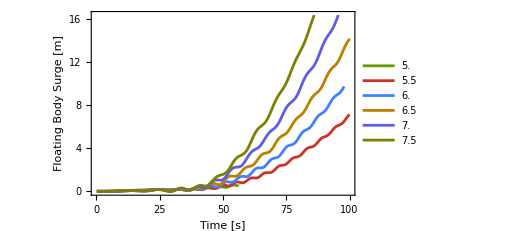

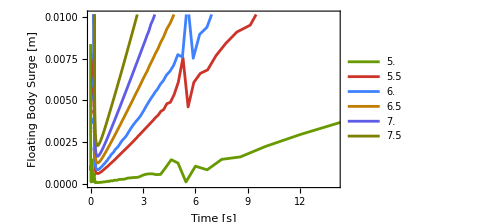

-Graphics3D-

```mathematica
ListPlot[Table[Transpose[{"time"/.d,("floatingbody_COM"/.d)ᵀ[[1]]-200}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions
,FrameLabel->{"Time [s]","Floating Body Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
]

ListPlot[Table[Transpose[{getPeriod[d],fftSurge[d]}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions
,FrameLabel->{"Time [s]","Floating Body Surge [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]

ListPlot3D[Flatten[Table[Transpose[{getPeriod[d[[2]]],Table[d[[1]],{i,1,Length[getPeriod[d[[2]]]]}],fftSurge[d[[2]]]}],{d,Table[{T,data[T]},{T,Ts}]}],1],
PlotRange->{{0.1,14},{5,10},{0,4*10^-3}}
,Evaluate@commonOptions3D
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ColorFunction->"SouthwestColors"
]
```

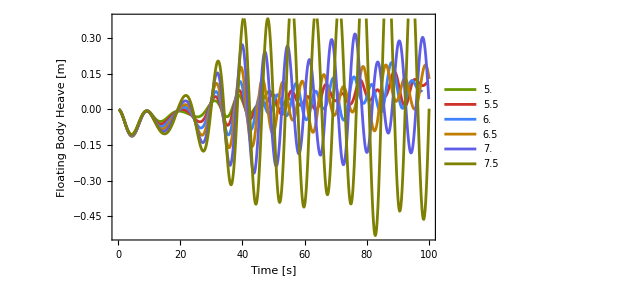

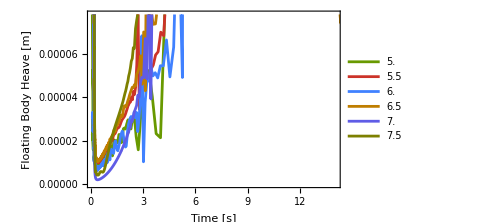

-Graphics3D-

```mathematica
ListPlot[Table[Transpose[{"time"/.d,("floatingbody_COM"/.d)ᵀ[[3]]-75}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions
,FrameLabel->{"Time [s]","Floating Body Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
]

ListPlot[Table[Transpose[{getPeriod[d],fftHeave[d]}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions
,FrameLabel->{"Time [s]","Floating Body Heave [m]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]

ListPlot3D[Flatten[Table[Transpose[{getPeriod[d[[2]]],Table[d[[1]],{i,1,Length[getPeriod[d[[2]]]]}],fftHeave[d[[2]]]}],{d,Table[{T,data[T]},{T,Ts}]}],1],
PlotRange->{{2,14},{5,10},{0,4*10^-3}}
,Evaluate@commonOptions3D
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ColorFunction->"SouthwestColors"
]
```

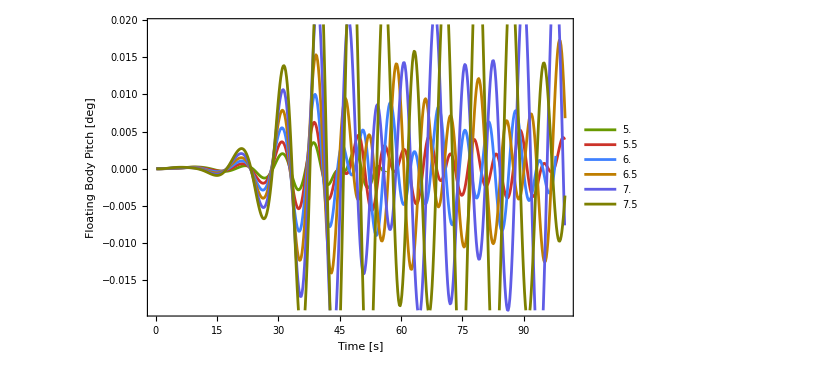

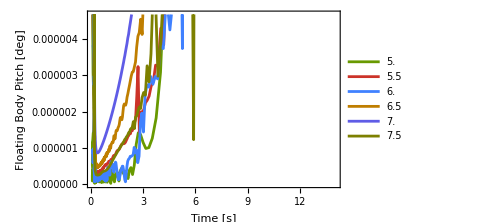

-Graphics3D-

```mathematica
ListPlot[Table[Transpose[{"time"/.d,"floatingbody_pitch"/.d}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions
,FrameLabel->{"Time [s]","Floating Body Pitch [deg]"}
,PlotLegends->Table[T,{T,Ts}]
]

ListPlot[Table[Transpose[{getPeriod[d],fftPitch[d]}],{d,Table[data[T],{T,Ts}]}]
,Evaluate@commonOptions
,FrameLabel->{"Time [s]","Floating Body Pitch [deg]"}
,PlotLegends->Table[T,{T,Ts}]
,PlotRange->{{0.1,14},Automatic}
]

ListPlot3D[Flatten[Table[Transpose[{getPeriod[d[[2]]],Table[d[[1]],{i,1,Length[getPeriod[d[[2]]]]}],fftPitch[d[[2]]]}],{d,Table[{T,data[T]},{T,Ts}]}],1],
PlotRange->{{2,14},{5,10},{0,4*10^-3}}
,Evaluate@commonOptions3D
,AxesLabel->{"Period [s]","Incident [m]","FFT"}
,ColorFunction->"SouthwestColors"
]
```